```mathematica
Clear[x,n]
h[x_]:= Sin[ ArcTan[E^x^2+Cos[3 x]]]-2 Cos[3 x]
x[0]=0.8;
x[n_]:=x[n]=x[n-1]- h[x[n-1]]/h'[x[n-1]]
Table[{x[n],h[x[n]]},{n,0,6}]
```

{{0.8,2.23194},{0.284986,-0.445382},{0.38799,0.0501956},{0.378371,0.000298528},{0.378313,1.13299×10^-8},{0.378313,2.22045×10^-16},{0.378313,-2.22045×10^-16}}

```mathematica
{0.6,0.37864785178294774,0.3783130759914863,0.37831300262357753,0.378313002623574,0.3783130026235739,0.378313002623574,0.3783130026235739,0.378313002623574,0.3783130026235739,0.378313002623574,0.3783130026235739,0.378313002623574}
```

{0.6,0.378648,0.378313,0.378313,0.378313,0.378313,0.378313,0.378313,0.378313,0.378313,0.378313,0.378313,0.378313}

```mathematica
{0.6,0.37864785178294774,0.3783130759914863,0.37831300262357753,0.378313002623574,0.3783130026235739}
```

$Aborted

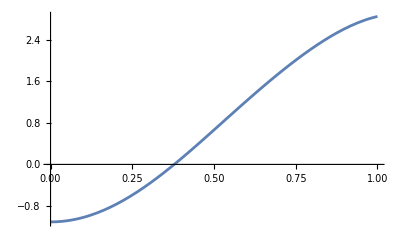

```mathematica
Plot[h[x],{x, 0,1}]
```